```mathematica
A=Import["/home/sudhir/Ashish/latest/9,8squareadj.txt","Table"];
```

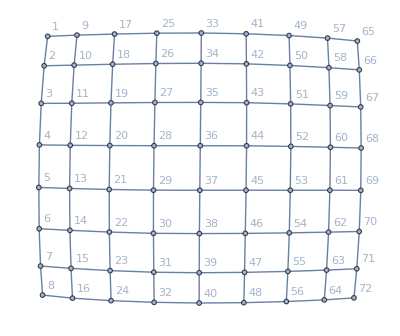

```mathematica
G1=AdjacencyGraph[A,VertexLabels->"Name"]
```

```mathematica
Q1=Import["/home/sudhir/Ashish/latest/9,8squaredeg.txt","Table"];
```

```mathematica
Q=Q1-IdentityMatrix[72];
```

```mathematica
f[x_]=((1-x^2)^(EdgeCount[G1]-VertexCount[G1]))*Det[IdentityMatrix[72]-x*A+x*x*Q];
```

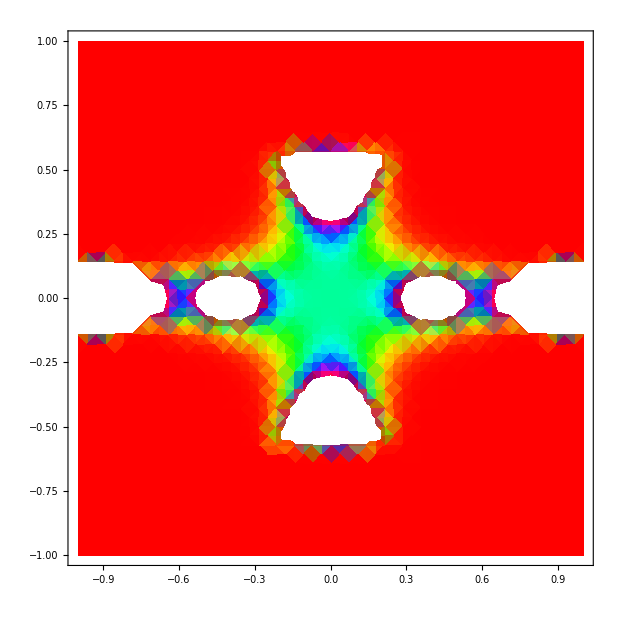

```mathematica
DensityPlot[1/Abs[f[xx+I*yy]],{xx,-1,1},{yy,-1,1},ColorFunction->Hue]
```

```mathematica
Plot3D[1/Abs[f[xx+I*yy]],{xx,-1,1},{yy,-1,1}]
```

-Graphics3D-

```mathematica
Plot3D[Abs[f[2^(-xx-I*yy)]],{xx,-1,1},{yy,-1,1}]
```

-Graphics3D-

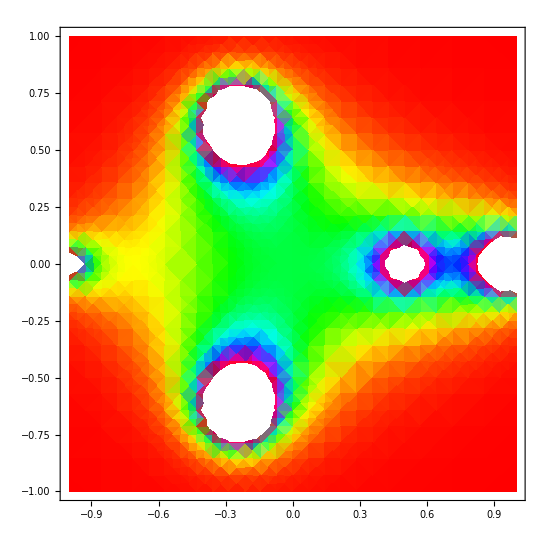

```mathematica
DensityPlot[1/Abs[(1-(x+ⅈ*y)^2)^2*(1-(x+ⅈ*y))*(1-2*(x+ⅈ*y))*(1+(x+ⅈ*y)+2*(x+ⅈ*y)^2)^3],{x,-1,1},{y,-1,1},ColorFunction->Hue]
```